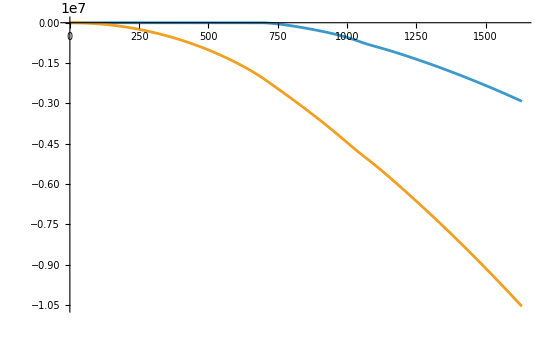

```mathematica
SetDirectory[NotebookDirectory[]];
Re1=Flatten[Import["Re.dat"]];
Im1=Flatten[Import["Im.dat"]];
omega=Flatten[Import["omega.dat"]];
mr2=Flatten[Import["mrho2bare.dat"]];
ListLinePlot[{Transpose[{omega,Im1}],Transpose[{omega,Re1}]},PlotRange->All(*,ScalingFunctions->{Automatic,Automatic}*)]
```